```mathematica
Clear All



Subscript[g, 1][n_]:=1;

Subscript[g, 2][m_]:=1;
s=√10;
r=√10;

l=50;
```

All Clear

```mathematica
Θ[τ_,p1_,p2_]:= τ/2 Cos[τ*(p1-p2)]-1/(4*p1)Sin[2*p1*τ];
Subscript[q, 1][n_]:=Exp[-Abs[s]^2/2]*s^n/(√(n!));
Subscript[q, 2][m_]:=Exp[-Abs[r]^2/2]*r^m/(√(m!));
```

```mathematica
f1[m_,n_]:=Subscript[g, 1][n+1]*Subscript[g, 2][m+1]*Sqrt[(n+1)*(m+1)];
f2[m_,n_]:=Subscript[g, 1][n+2]*Subscript[g, 2][m+2]*Sqrt[(n+2)*(m+2)];
f[m_,n_]:=Sqrt[f1[m,n]^2+f2[m,n]^2];
```

```mathematica
A[m_,n_,τ_,p1_,p2_]:=f1[m,n]^2/f[m,n]^2*Cos[2*Θ[τ,p1,p2]*f[m,n]]+f2[m,n]^2/f[m,n]^2;
```

```mathematica
B[m_,n_,τ_,p1_,p2_]:=-(I*f1[m,n])/(2*f[m,n])*Sin[2*Θ[τ,p1,p2]*f[m,n]];
```

```mathematica
Dm[m_,n_,τ_,p1_,p2_]:=-(I*f1[m,n])/(2*f[m,n])*Sin[2*Θ[τ,p1,p2]*f[m,n]];
```

```mathematica
Fm[m_,n_,τ_,p1_,p2_]:=(f1[m,n]*f2[m,n])/(2*f[m,n]^2)*(Cos[2*Θ[τ,p1,p2]*f[m,n]^2]-1);
```

```mathematica
k[m_,n_,τ_,p1_,p2_]:=(f1[m,n]*f2[m,n])/(2*f[m,n]^2)*(Cos[2*Θ[τ,p1,p2]*f[m,n]^2]-1);
```

```mathematica
NN[m_,n_,τ_,p1_,p2_]:=(f1[m,n]*f2[m,n])/(2*f[m,n]^2)*(Cos[2*Θ[τ,p1,p2]*f[m,n]^2]-1);
```

```mathematica
nf[τ_,p1_,p2_]:=(∑_(n=0)^l ∑_(m=0)^l Abs[Subscript[q, 1][n]]^2*Abs[Subscript[q, 2][m]]^2*(Abs[A[m,n,τ,p1,p2]]^2+2*Abs[B[m,n,τ,p1,p2]]^2+2*Abs[Dm[m,n,τ,p1,p2]]^2+Abs[Fm[m,n,τ,p1,p2]]^2+2*Abs[k[m,n,τ,p1,p2]]^2+Abs[NN[m,n,τ,p1,p2]]^2))^(-1);
```

```mathematica
R1[m_,n_,τ_,p1_,p2_]:=nf[τ,p1,p2]*∑_(n=0)^l ∑_(m=0)^l Subscript[q, 1][n+2]*Conjugate[Subscript[q, 1][n]]*Conjugate[Subscript[q, 2][m]]*Subscript[q, 2][m+2]*(Conjugate[A[m,n,τ,p1,p2]]*A[m+2,n+2,τ,p1,p2]*Sqrt[(n+2)*(n+1)*(m+2)*(m+1)]+2*Conjugate[B[m,n,τ,p1,p2]]*B[m+2,n+2,τ,p1,p2]*Sqrt[(n+3)*(n+2)*(m+3)*(m+2)]+2*Conjugate[Dm[m,n,τ,p1,p2]]*Dm[m+2,n+2,τ,p1,p2]*Sqrt[(n+3)*(n+2)*(m+3)*(m+2)]+2*Conjugate[k[m,n,τ,p1,p2]]*k[m+2,n+2,τ,p1,p2]*Sqrt[(n+3)*(n+4)*(m+3)*(m+4)]+Conjugate[Fm[m,n,τ,p1,p2]]*Fm[m+2,n+2,τ,p1,p2]*Sqrt[(n+3)*(n+4)*(m+3)*(m+4)]+Conjugate[NN[m,n,τ,p1,p2]]*NN[m+2,n+2,τ,p1,p2]*Sqrt[(n+3)*(n+4)*(m+3)*(m+4)]);
```

```mathematica
R2[m_,n_,τ_,p1_,p2_]:=nf[τ,p1,p2]*∑_(n=0)^l ∑_(m=0)^l Abs[Subscript[q, 1][n]]^2*Abs[Subscript[q, 2][m]]^2*(n*m*Abs[A[m,n,τ,p1,p2]]^2+2*(n+1)*(m+1)*(Abs[B[m,n,τ,p1,p2]]^2+Abs[Dm[m,n,τ,p1,p2]]^2)+2*(n+2)*(m+2)*Abs[k[m,n,τ,p1,p2]]^2+(n+2)*(m+2)*Abs[Fm[m,n,τ,p1,p2]]^2+(n+2)*(m+2)*Abs[NN[m,n,τ,p1,p2]]^2);
```

```mathematica
R3[m_,n_,τ_,p1_,p2_]:=nf[τ,p1,p2]*∑_(n=0)^l ∑_(m=0)^l Subscript[q, 2][m+1]*Conjugate[Subscript[q, 2][m]]*Conjugate[Subscript[q, 1][n]]*Subscript[q, 1][n+1]*(Conjugate[A[m,n,τ,p1,p2]]*A[m+1,n+1,τ,p1,p2]*Sqrt[(n+1)*(m+1)]+2*Conjugate[B[m,n,τ,p1,p2]]*B[m+1,n+1,τ,p1,p2]*Sqrt[(n+2)*(m+2)]+2*Conjugate[Dm[m,n,τ,p1,p2]]*Dm[m+1,n+1,τ,p1,p2]*Sqrt[(n+2)*(m+2)]+2*Conjugate[k[m,n,τ,p1,p2]]*k[m+1,n+1,τ,p1,p2]*Sqrt[(n+3)*(m+3)]+Conjugate[Fm[m,n,τ,p1,p2]]*Fm[m+1,n+1,τ,p1,p2]*Sqrt[(n+3)*(m+3)]+Conjugate[NN[m,n,τ,p1,p2]]*NN[m+1,n+1,τ,p1,p2]*Sqrt[(n+3)*(m+3)]);
```

```mathematica
R4[m_,n_,τ_,p1_,p2_]:=nf[τ,p1,p2]*∑_(n=0)^l ∑_(m=0)^l Abs[Subscript[q, 1][n]]^2*Abs[Subscript[q, 2][m]]^2*(n*Abs[A[m,n,τ,p1,p2]]^2+2*(n+1)*(Abs[B[m,n,τ,p1,p2]]^2+Abs[Dm[m,n,τ,p1,p2]]^2)+2*(n+2)*Abs[k[m,n,τ,p1,p2]]^2+(n+2)*Abs[Fm[m,n,τ,p1,p2]]^2+(n+2)*Abs[NN[m,n,τ,p1,p2]]^2);
```

```mathematica
R5[m_,n_,τ_,p1_,p2_]:=nf[τ,p1,p2]*∑_(n=0)^l ∑_(m=0)^l Abs[Subscript[q, 1][n]]^2*Abs[Subscript[q, 2][m]]^2*(m*Abs[A[m,n,τ,p1,p2]]^2+2*(m+1)*(Abs[B[m,n,τ,p1,p2]]^2+Abs[Dm[m,n,τ,p1,p2]]^2)+2*(m+2)*Abs[k[m,n,τ,p1,p2]]^2+(m+2)*Abs[Fm[m,n,τ,p1,p2]]^2+(m+2)*Abs[NN[m,n,τ,p1,p2]]^2);
```

```mathematica
Ent[τ_,p1_,p2_] :=Module[{a1,a2,a3,a4,a5}, a1 = R1[m,n,τ,p1,p2];  a2 = R2[m,n,τ,p1,p2]; a3=R3[m,n,τ,p1,p2];a4=R4[m,n,τ,p1,p2];a5=R5[m,n,τ,p1,p2];(2*Re[a1]+2*a2-4*(Re[a3])^2)/(a4+a5+1)];
```

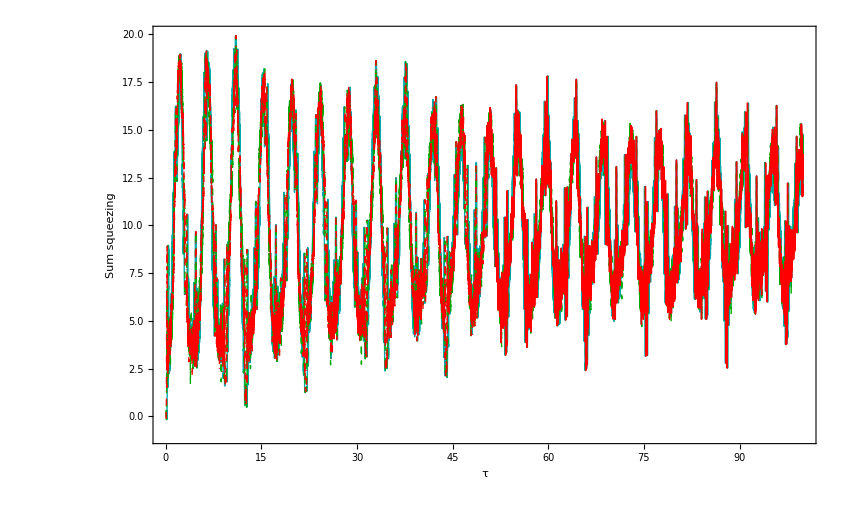

```mathematica
a=Re[Ent[τ,2,2]];
b=Re[Ent[τ,4,4]];
c=Re[Ent[τ,6,6]];
multient=Plot[{a,b,c},{τ,0,100},PlotRange->{{0,100},{-1,20}},Frame->True,FrameLabel->{τ,"Sum squeezing "},RotateLabel->True,PlotStyle->{{Darker[Cyan]},{Darker[Green],Dashed},{Red,DotDashed}},PlotPoints->500,ImageSize->850,LabelStyle->Directive[Green,35],FrameStyle->Directive[Blue,AbsoluteThickness[4]]]
```

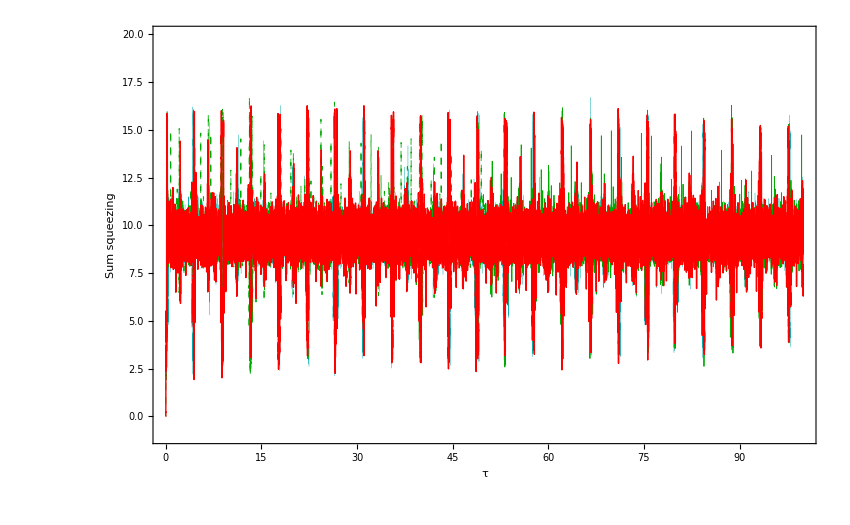

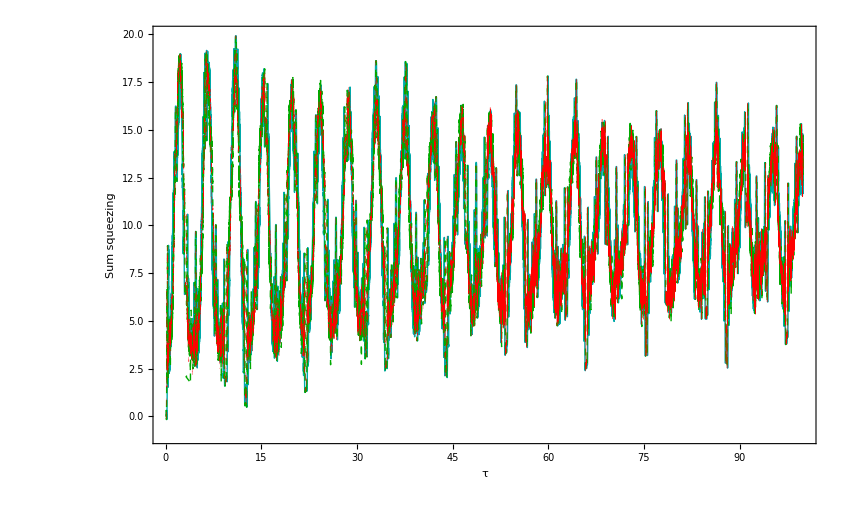

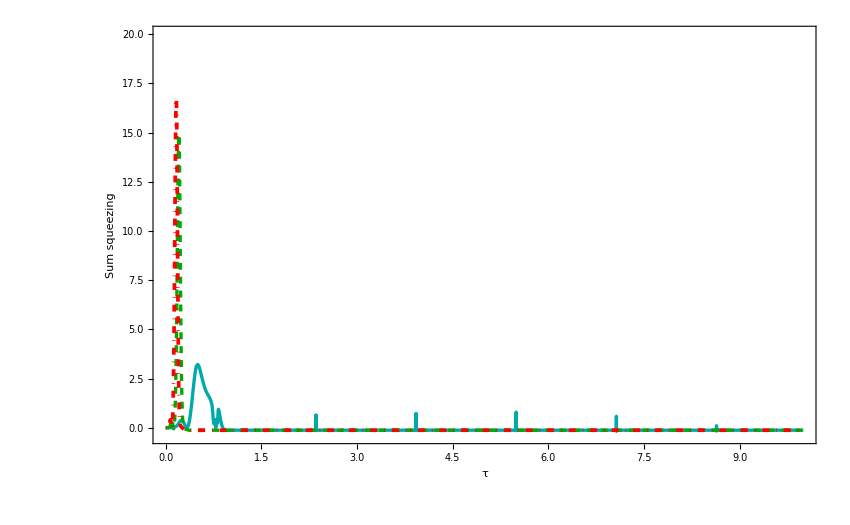

```mathematica
Show[multient,PlotRange->{{0,10},{-0.4,0.6}}]
```

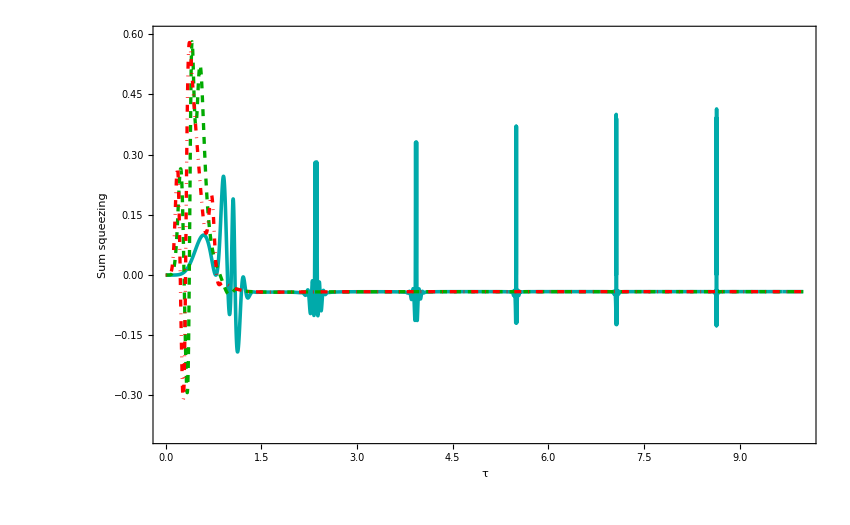

```mathematica
Show[multient,PlotRange->{{0,10},{-0.3,5}}]
```